## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
data=Import["junk.csv"];
```

```mathematica
data=Import["guerra-summer-2011-kc-opps.csv"];
```

```mathematica
Take[data,5]
```

{{accel-at-rest,asu_9Q1920841f2ca4d1fasul1_c,md5:1da7d76bc3d524d51da47dde26ee8f95,0,1},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_e,md5:e3e61859acb08ee896e06e1020f95a49,0},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e66c328693800f93b41f13d97b78e19b,1},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e9747bab59caf0446778cc6a65a8ac2e,0}}

### Fitting routines

```mathematica
logistic[n_,{mu_,b_}]:=1/(Exp[-b  n+mu]+1); (* this choice of parameters gives finite constraint region *)
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl+1/2]+1) (1-ps-pg)/2;
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b n];
(* For testing *)
linear[n_,{a_,b_}]:=a n + b;
```

```mathematica
stepFit[data_]:=Block[{best=-Infinity,lBest},Do[Block[{l0=Count[Take[data,i],0,1],l1=Count[Take[data,i],1,1],u0=Count[Drop[data,i],0,1],u1=Count[Drop[data,i],1,1],g,s,logLike=0},If[l0+l1>0,g=l1/(l0+l1);logLike+=If[l1>0,l1*Log[g],0]+If[l0>0,l0*Log[1-g],0]];If[u0+u1>0,s=u0/(u0+u1);logLike+=If[u0>0,u0*Log[s],0]+If[u1>0,u1*Log[1-s],0]];
	(*Print[{i,g,s,logLike}]; *)If[logLike>best,best=logLike;lBest=i]],{i,0,Length[data]-1}];If[Length[data]≥3,2*3-2*N[best]]]
```

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[Log[If[data[[i]]==1,model[i-1,params],1-model[i,params]]],{i,Length[data]}]
maxer[model_,vars_,constraints_,data_]:=Which[
(* too few data points *)
Length[data]<Length[vars],Null,
(* All three functions can perfectly fit to all ones or zeros, but numerical fit is hard. *)
Count[data,0,1]==0 || Count[data,1,1]==0,2 Length[vars],True,
Block[{x=NMaximize[{logProb[model,vars,data],constraints[data]},vars,Method->{"RandomSearch",Method->"ConjugateGradient"}]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[data,x];False]]]
```

```mathematica
logisticConstraints[x_]:=Block[{delta=15,ones=Position[x,1,1],zeros=Position[x,0,1]},mu≥Max[zeros[[-1,1]]*b,zeros[[1,1]]*b]-delta&& mu≤Min[ones[[1,1]]*b,ones[[-1,1]]*b]+delta&& b>-2 delta/Max[1,ones[[-1,1]]-zeros[[1,1]]] && b<2 delta/Max[1,zeros[[-1,1]]-ones[[1,1]]]]
```

```mathematica
bktConstraints[_]:=Block[{delta=15},pg≥Exp[-delta] && ps≥Exp[-delta] && pg≤1-Exp[-delta] && ps≤ 1-Exp[-delta] &&b≥0 && b<delta]
```

```mathematica
linearConstraints[x_]:=Block[{delta=15},b≥Exp[-delta] && b≤1-Exp[-delta] && a>=(Exp[-delta]-b)/Length[x] && a<=(1-Exp[-delta]-b)/Length[x]]
```

Correction to get AIC_c

```mathematica
aicCorrection[k_,n_]:=2 k (k+1)/(n-k-1)
```

### Stuff

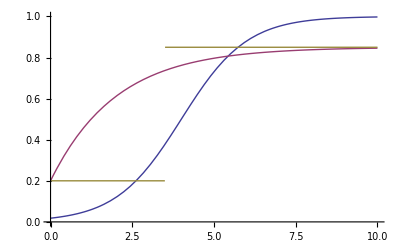

```mathematica
Plot[{logistic[x,{4,1}],bkt[x,{.5,.2,.15}],step[x,{4,.2,.15}]},{x,0,10},PlotRange->{0,1}]
```

```mathematica
TableForm[Map[{#[[1]],stepFit[Drop[#,3]]}&,data]]
```

accel-constant-speed | Null
area-of-circle | Null
bernoulli | 6.
combo-magnification | Null
compo-general-case | 32.9921
compo-general-case-unknown | Null
compo-parallel-axis | 82.3817
compo-perpendicular | 39.1042
compo-z-axis | 16.585
compo-zero-vector | Null
continuity | Null
define-angle-between-lines | 6.
define-angular-frequency | 9.81909
define-area | Null
define-area-at | Null
define-charge | 28.4934
define-coef-friction | Null
define-compression | Null
define-current-thru | 17.4573
define-distance | 6.
define-distance-between | 9.81909
define-duration | 21.2763
define-electric-power-var | 6.
define-energy-var | Null
define-flux | Null
define-focal-length | 6.
define-frequency | 20.0453
define-grav-accel | 6.
define-image-distance | 8.77259
define-index-of-refraction | 6.
define-magnification | 6.
define-mass | 18.3152
define-mass-density | 6.
define-moment-of-inertia | 6.
define-object-distance | 6.
define-period-var | 8.77259
define-pressure | 15.5607
define-radius-of-circle | 6.
define-resistance-var | 14.9974
define-revolution-radius | 6.
define-shape-length | 6.
define-slit-separation | Null
define-speed | 8.77259
define-spring-constant | 8.77259
define-stored-energy-var | Null
define-turns | Null
define-voltage-across | 23.1989
define-volume | Null
define-wavelength | 6.
define-work | 8.77259
definition-syntax | 6.
draw-accel-free-fall | 6.
draw-accel-slow-down | Null
draw-accel-speed-up | 13.6382
draw-ang-accel | Null
draw-ang-accel-speed-up | Null
draw-ang-displacement-unknown | Null
draw-ang-momentum-rotating | 6.
draw-ang-velocity-rotating | 6.
draw-applied-force | 6.
draw-bfield-straight-current | 8.77259
draw-bforce-charge | 6.
draw-bforce-rhr-zero | Null
draw-bforce-unknown-velocity | Null
draw-body | 63.6435
draw-buoyant-force | Null
draw-centripetal-acceleration | 8.77259
draw-compo-form-axes | 17.4573
draw-coulomb-force-unknown | 6.
draw-displacement-given-dir | 8.77259
draw-displacement-straight | 10.4987
draw-displacement-unknown | Null
draw-displacement-zero | Null
draw-electric-force-given-field-dir | Null
draw-electric-force-given-field-unknown | Null
draw-energy-axes | 6.
draw-field-given-dir | 9.81909
draw-field-unknown | Null
draw-grav-force | Null
draw-impulse-given-momenta | Null
draw-kinetic-friction | Null
draw-line-given-dir | 13.6382
draw-line-unknown-dir | 6.
draw-momentum-at-rest | Null
draw-momentum-straight | 13.6382
draw-net-field-given-dir | 6.
draw-net-field-given-zero | Null
draw-net-field-unknown | Null
draw-net-force-from-accel | Null
draw-net-force-from-forces | Null
draw-net-force-unknown | Null
draw-normal | 10.4987
draw-point-efield-unknown | Null
draw-projection-axes | 6.
draw-relative-position | 8.77259
draw-relative-position-unknown | 6.
draw-spring-force | Null
draw-tension | 15.5607
draw-torque | Null
draw-unrotated-axes | 25.8748
draw-vector-aligned-axes | 6.
draw-velocity-at-rest | 9.81909
draw-velocity-curved | 14.9974
draw-velocity-curved-unknown | Null
draw-velocity-momentarily-at-rest | 10.4987
draw-velocity-straight | 39.5434
draw-velocity-straight-unknown | Null
draw-weight | 17.1624
draw-xy-vector-given-compos | Null
draw-z-axis-vector-given-compos | Null
equation-syntax | 30.356
equiv-resistance-parallel | 9.81909
equiv-resistance-series | 6.
kinetic-friction-law | Null
lens-combo | Null
lens-eqn | 9.81909
magnification-eqn | 6.
object-label | 6.
pendulum-oscillation | Null
pressure-at-open-to-atmosphere | 6.
pressure-force | Null
pressure-height-fluid | Null
sdd-constvel-compo | 9.81909
select-mc-answer | 65.5343
spring-law-compression | Null
spring-mass-oscillation | Null
write-ang-momentum | 6.
write-angle-direction-known-lines | 6.
write-archimedes | Null
write-average-rate-of-change | Null
write-cap-energy | Null
write-capacitance-definition | 6.
write-centripetal-accel | 6.
write-change-me | Null
write-charge-force-bfield | 8.77259
write-charge-force-bfield-mag | Null
write-charge-force-efield-compo | 6.
write-charge-force-efield-mag | Null
write-charge-same-caps-in-branch | Null
write-connected-accels | Null
write-cons-angmom | Null
write-cons-linmom-compo-join-split | Null
write-coulomb | Null
write-coulomb-compo | 6.
write-density | Null
write-electric-power | 8.77259
write-energy-cons | 6.
write-equality | 6.
write-faradays-law | Null
write-flux-constant-field | Null
write-flux-zero | Null
write-free-fall-accel | 6.
write-g-on-earth | Null
write-grav-energy | 11.004
write-harmonic-of | 6.
write-height-dy | Null
write-i-hoop-cm | Null
write-impulse-compo | Null
write-impulse-momentum-compo | Null
write-inside-solenoid-bfield | Null
write-junction-rule | Null
write-junction-rule-cap | Null
write-kinetic-energy | 15.5607
write-known-value-eqn | 235.968
write-linear-vel | Null
write-lk-no-s-compo | 14.3758
write-lk-no-t-compo | Null
write-lk-no-vf-compo | 10.4987
write-loop-rule-capacitors | 11.7416
write-loop-rule-resistors | 10.4987
write-mag-torque | Null
write-mass-compound | Null
write-momentum-compo | 6.
write-net-field-compo | Null
write-net-force-compo | 9.81909
write-nfl-compo | 12.7301
write-nsl-compo | 21.0257
write-nsl-rot-compo | Null
write-null-spring-energy | Null
write-ohms-law | 17.2868
write-period-circular | Null
write-point-charge-efield-compo | 6.
write-potential-energy | Null
write-right-triangle-tangent | Null
write-rk-no-s | Null
write-rk-no-vf | Null
write-sdd | 8.77259
write-single-loop-rule | Null
write-slit-interference | 6.
write-snells-law | Null
write-spring-energy | 8.77259
write-straight-wire-bfield | Null
write-sum-disp-compo | Null
write-sum-times | Null
write-tensions-equal | 6.
write-total-energy-top | 15.5607
write-transformer-power | Null
write-turns-per-length | Null
write-ug | Null
write-unit-vector-mag | Null
write-vector-magnitude | 6.
write-wave-speed-light | Null
write-wnc | Null
write-work | 6.
wt-law | 17.4573

Add AIC values for all sets with 3 or more points

```mathematica
aics=Apply[Plus,Map[If[Length[Drop[#,3]]≥3,{maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]],stepFit[Drop[#,3]]},0]&,data]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30.`, -183.55689551959716`}.

General::stop: Further output of Experimental`NumericalFunction will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize will be suppressed during this calculation.

$Aborted

### Generate random data and table of AIC' s

```mathematica
data=Table[Join[{Null,Null,Null},Table[RandomInteger[],{RandomInteger[{2,20}]}]],{10}]
```

{{Null,Null,Null,0,0,1,0,1},{Null,Null,Null,0,0,0,1,1,0,0,1,0,1,0,0},{Null,Null,Null,0,0,1,0,0,1,0},{Null,Null,Null,0,0,1,0,1,1,1,1,1,0,0},{Null,Null,Null,1,0,0,0,0,1,1,1,0,1,1,0,1,1},{Null,Null,Null,1,0,1,0,1,0},{Null,Null,Null,1,1},{Null,Null,Null,0,0,1,1,0,1,1,0,1,1,0,1},{Null,Null,Null,1,0,0,0,1,1},{Null,Null,Null,1,1,1,1,0,0,1,0,1,0,0,0,1,1,1,0}}

Make exponential data

```mathematica
data=Table[Join[{Null,Null,Null},Block[{a=Random[],b=Random[],c=2*Random[],n=RandomInteger[{100,500}]},Table[If[Random[]>a+(b-a) Exp[-c i/n],1,0],{i,n}]]],{50}]
```

{{Null,Null,Null,0,1,1,1,0,1,0,0,1,1,1,1,1,1,0,0,1,0,0,0,1,1,1,0,1,1,1,1,1,0,0,1,0,0,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,1,1,1,1,0,0,1,1,1,0,1,1,0,1,0,1,1,1,1,0,1,1,1,1,0,0,0,1,0,0,1,1,0,1,1,1,0,0,0,0,1,1,1,1,1,1,0,1,1,1,1,1,0,1,0,0,0,1,1,1,1,1,1,0,0,1,1,0,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,0,1,1,1,0,0,0,1,1,1,1,0,0,1,1,1},«49»}

### Generate full table of AIC' s

```mathematica
TableForm[allValues=Map[{#[[1]],#[[3]],Length[Drop[#,3]],Print[#[[1]]," logistic ",#[[3]]];maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],stepFit[Drop[#,3]],Print[#[[1]]," bkt ",#[[3]]];maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]]}&,data]]
```

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null | Null | 163 | 212.277 | 211.306 | 214.41
Null | Null | 355 | 463.606 | 464.332 | 466.015
Null | Null | 122 | 91.8596 | 92.5963 | 95.3764
Null | Null | 105 | 133.687 | 132.836 | 134.386
Null | Null | 391 | 532.939 | 526.541 | 530.058
Null | Null | 192 | 241.687 | 238.833 | 242.557
Null | Null | 382 | 452.053 | 452.804 | 474.323
Null | Null | 329 | 441.007 | 438.523 | 442.35
Null | Null | 404 | 466.665 | 464.984 | 470.679
Null | Null | 462 | 365.194 | 365.601 | 370.32
Null | Null | 202 | 261.938 | 262.183 | 283.804
Null | Null | 426 | 590.67 | 587.891 | 595.116
Null | Null | 215 | 288.35 | 281.432 | 283.248
Null | Null | 316 | 403.011 | 402.679 | 400.895
Null | Null | 410 | 428.842 | 427.159 | 432.378
Null | Null | 319 | 417.595 | 416.989 | 419.44
Null | Null | 102 | 143.443 | 140.309 | 143.78
Null | Null | 443 | 607.611 | 602.534 | 607.895
Null | Null | 284 | 372.847 | 369.886 | 376.078
Null | Null | 386 | 514.436 | 507.208 | 511.929
Null | Null | 193 | 197.028 | 194.144 | 202.227
Null | Null | 189 | 252.762 | 254.077 | 254.919
Null | Null | 369 | 164.624 | 163.365 | 166.894
Null | Null | 475 | 661.254 | 658.258 | 662.544
Null | Null | 143 | 198.525 | 191.588 | 199.432
Null | Null | 294 | 375.099 | 372.782 | 374.091
Null | Null | 272 | 356.837 | 354.787 | 355.426
Null | Null | 279 | 361.595 | 357.879 | 363.355
Null | Null | 259 | 329.604 | 326.791 | 330.125
Null | Null | 329 | 428.85 | 431.072 | 431.294
Null | Null | 494 | 684.29 | 681.824 | 688.687
Null | Null | 400 | 555.671 | 555.442 | 557.928
Null | Null | 308 | 382.767 | 378.506 | 380.491
Null | Null | 355 | 453.647 | 453.366 | 456.041
Null | Null | 461 | 634.311 | 633.412 | 638.689
Null | Null | 309 | 286.568 | 286.636 | 288.686
Null | Null | 261 | 269.471 | 270.452 | 271.615
Null | Null | 219 | 214.232 | 209.666 | 222.501
Null | Null | 367 | 491.014 | 490.067 | 496.373
Null | Null | 343 | 443.437 | 440.779 | 445.039
Null | Null | 179 | 246.009 | 245.484 | 247.442
Null | Null | 112 | 155.276 | 155.152 | 157.221
Null | Null | 283 | 331.027 | 329.531 | 332.249
Null | Null | 221 | 239.971 | 240.408 | 239.628
Null | Null | 340 | 382.625 | 398.488 | 380.467
Null | Null | 381 | 497.781 | 497.894 | 500.919
Null | Null | 422 | 529.094 | 530.617 | 530.874
Null | Null | 426 | 430.749 | 433.2 | 432.941
Null | Null | 210 | 264.027 | 254.529 | 254.678
Null | Null | 388 | 334.713 | 327.668 | 335.623

```mathematica
Save["fitAll.m",allValues]
```

### Analyze

Logistic, step model, Baysian Knowledge Tracing

```mathematica
Get["fitAll.m"];
```

```mathematica
allValues[[1]]
```

{Null,Null,163,212.277,211.306,214.41}

```mathematica
Length[cutValues=Select[allValues,#[[3]]≥6&]]
```

50

```mathematica
Length[Union[Map[First,cutValues]]]
```

1

```mathematica
Length[Union[Map[#[[2]]&,cutValues]]]
```

1

```mathematica
% %%
```

456

```mathematica
aics=Map[{#[[4]]+aicCorrection[2,#[[3]]],#[[5]]+aicCorrection[3,#[[3]]],#[[6]]+aicCorrection[3,#[[3]]]}&,cutValues];
```

```mathematica
akaikeWeights=Map[Block[{y=Exp[-#/2]},y/Apply[Plus,y]]&,aics];
```

```mathematica
akaikeRawWeights=Map[Block[{y=Exp[-#/2]},y/Apply[Plus,y]]&,Map[Drop[#,3]&,cutValues]];
```

```mathematica
Map[{Median[#],Mean[#],StandardDeviation[#]/Length[#]}&,Transpose[akaikeWeights]]
```

{{0.283646,0.291688,0.00359384},{0.559,0.560622,0.00444989},{0.118379,0.14769,0.0029471}}

```mathematica
Map[{Median[#],Mean[#],StandardDeviation[#]/Length[#]}&,Transpose[akaikeRawWeights]]
```

{{0.279972,0.287537,0.00356165},{0.562636,0.563787,0.00444033},{0.119556,0.148677,0.00295973}}

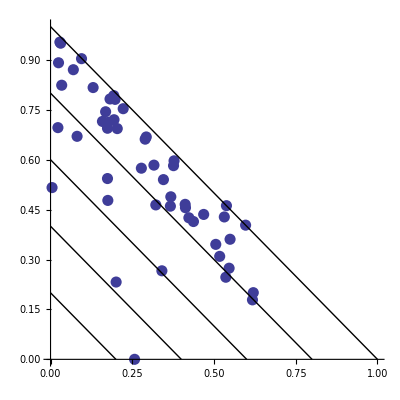

```mathematica
ListPlot[Map[Take[#,2]&,akaikeWeights],AspectRatio->1,PlotStyle->{PointSize[0.02]},Epilog->Table[Line[{{0,i},{i,0}}],{i,0,1,1/5}],PlotRange->{{0,1},{0,1}}]
```

```mathematica
Histogram3D[Map[Take[#,2]&,akaikeWeights],{{0,1,0.02},{0,1,0.02}},PlotRange->{{0,1},{0,1},All}]
```

-Graphics3D-

```mathematica
hc=Histogram[Transpose[akaikeWeights],20,"Count",PlotRange->All,ChartLegends->{"logistic","step","BKT"},Axes->False,Frame->True,FrameLabel->{"Akaike weight","number of student-KCs"}]
```

-Graphics--Graphics- | logistic
-Graphics- | step
-Graphics- | BKT

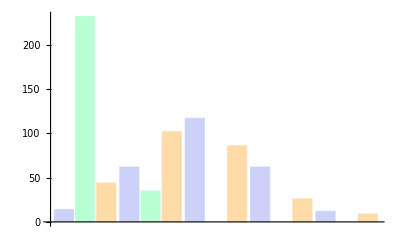
-Graphics--Graphics- | logistic
-Graphics- | BKT
-Graphics- | step

```mathematica
bc=BarChart[{{14,232,44},{62,35,102},{117,0,86},{62,0,26},{12,0,9}},ChartLegends->Placed[{"logistic","BKT","step"},{{0.5,0.5}}]]
```

```mathematica
Overlay[{bc[[1]],bc[[2]]},Alignment->{0.75,0.75}]
```

-Graphics--Graphics- | logistic
-Graphics- | BKT
-Graphics- | step